# KASUS TOV GR constant energy density

## Backward lalu Forward

### Backward calculation

```mathematica
Clear["Global`*"]
```

```mathematica
B=60.
ϵ[p_]=0 p+4B (* Model Quark Star *)
dϵdp=D[ϵ[p],p];
```

60.

240.

```mathematica
eq1[r_]=(4 π r^3 p[r]+m[r])(2GS)/(r (r-2 GS m[r]));
(*Persamaan differensial metrik*)
eq2[r_]=-m'[r]+4 π r^2 ϵ[p[r]];(*Persamaan differensial massa*)
eq3[r_]=-p'[r]- eq1[r](ϵ[p[r]]+p[r])/2 ; (*Persamaan TOV*)
```

```mathematica
GS=1.325*10^-12; (* Konstanta gravitasi *)
MSS= 1.1155 * 10^15; (* Massa matahari *)
```

```mathematica
rmax0=10^(-3);
M=MSS*2.61; (* Massa di permukaan *)
k=0.541276549838625;
R=(2 GS M)/k;(* radius di permukaan *)
PCC=1.*^-15; (* Tekanan di permukaan *)

r00=R;
MCC=M;
(*NumberForm[{r00,R},20]
NumberForm[{(MCC/MSS),(M/MSS)},20]*)

Clear[rStar2];
state=First[NDSolve`ProcessEquations[{ν'[r]==2 eq1[r],eq2[r]==0,eq3[r]==0,ν[r00]==Log[1-2GS MCC/r00] ,m[r00]==MCC , p[r00]==PCC},{ν,m,p},{r,r00,rmax0},Method->{"EventLocator","Event" :>{r-1.0001 2GS m[r]},"EventAction":>Throw[rStar2=r,"StopIntegration"]}]];
NDSolve`Iterate[state,rmax0]
solb=NDSolve`ProcessSolutions[state]

moo[r_]=Evaluate[m[r]/. solb];
poo[r_]=Evaluate[p[r]/. solb];
νoo[r_]=Evaluate[ν[r]/. solb];

NumberForm[poo'[rmax0],12]
```

{ν→InterpolatingFunction[{{0.001, 14254.}}, <>],m→InterpolatingFunction[{{0.001, 14254.}}, <>],p→InterpolatingFunction[{{0.001, 14254.}}, <>]}

-71.2938497223

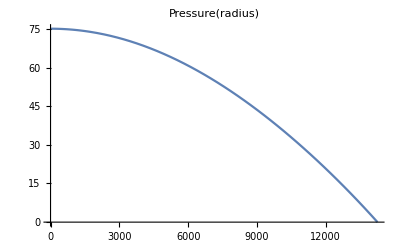

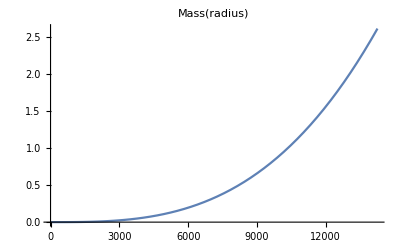

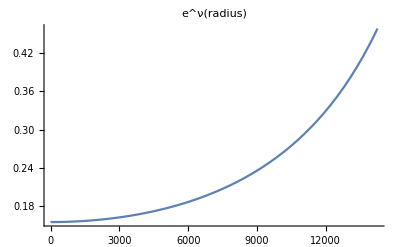

```mathematica
mStar=moo[rStar];
Plot[{poo[r]},{r,rmax0,r00},PlotRange->All,PlotLabel->Pressure[radius]]
Plot[{moo[r]/MSS},{r,rmax0,r00},PlotRange->All,PlotLabel->Mass[radius]]
Plot[{Exp[νoo[r]]},{r,rmax0,r00},PlotRange->All,PlotLabel->(e^ν)[radius]]
```

```mathematica
{rmax0,poo[rmax0],moo[rmax0]/MSS}
{r00,moo[r00]/MSS,poo[r00]}
```

{1/1000,75.129,1.52997×10^-10}

{14254.,2.61,1.×10^-15}

### Reverse calculation

```mathematica
r0=rmax0;(* radius di pusat *)
rmax=100000.;
MCC=moo[rmax0]; (* Massa di pusat *)
PCC=poo[rmax0]; (* Tekanan di pusat *)
```

```mathematica
Clear[rStar];
state=First[NDSolve`ProcessEquations[{ν'[r]==2 eq1[r],eq2[r]==0,eq3[r]==0,ν[r0]==0. ,m[r0]==MCC , p[r0]==PCC},{ν,m,p},{r,r0,rmax},Method->{"EventLocator","Event" :>{p[r]},"EventAction":>Throw[rStar=r,"StopIntegration"]}]];
NDSolve`Iterate[state,rmax]
solf=NDSolve`ProcessSolutions[state]
rStar
```

{ν→InterpolatingFunction[{{0.001, 14254.}}, <>],m→InterpolatingFunction[{{0.001, 14254.}}, <>],p→InterpolatingFunction[{{0.001, 14254.}}, <>]}

14254.

```mathematica
mo[r_]=Evaluate[m[r]/. solf];
po[r_]=Evaluate[p[r]/. solf];
νo[r_]=Evaluate[ν[r]/. solf];
k=Log[1-2GS mo[rStar]/rStar]-νo[rStar]
νo[r_]=νo[r]+k;
```

-1.86868

14254.001438959296     2.610000985549952     240.     75.129

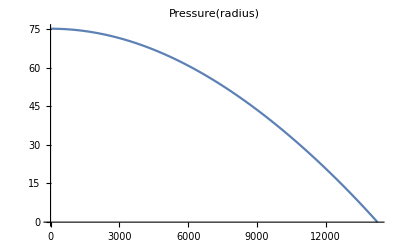

-Graphics-

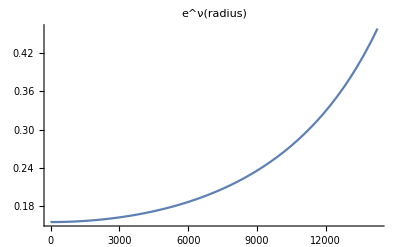

```mathematica
mStar=mo[rStar];
(*Print[rStar,"     ",mStar/MSS,"     ",ϵ[p[r0]],"     ",PCC]*)
Print[FortranForm[rStar],"     ",FortranForm[mo[rStar]/MSS],"     ",ϵ[po[r0]],"     ",PCC]
Plot[{po[r]},{r,r0,rStar},PlotRange->All,PlotLabel->Pressure[radius]]
Plot[{mo[r]/MSS},{r,r0,rStar},PlotRange->All,PlotLabel->Mass[radius]]
Plot[{Exp[νo[r]]},{r,r0,rStar},PlotRange->All,PlotLabel->(e^ν)[radius]]
```

```mathematica
{r0,po[r0],mo[r0]/MSS}
{rStar,mo[rStar]/MSS,po[rStar]}
```

{1/1000,75.129,1.52997×10^-10}

{14254.,2.61,-2.9976×10^-15}

### Perbandingan

```mathematica
(* backward *) 

NumberForm[{rmax0,moo[rmax0]/MSS,poo[rmax0]},12]
NumberForm[{r00,moo[r00]/MSS,poo[r00]},12]
```

{1/1000,1.52996576474×10^-10,75.129048396}

{14253.9996464,2.61,1.×10^-15}

```mathematica
(* forward *) 

NumberForm[{r0,mo[r0]/MSS,po[r0]},12]
NumberForm[{rStar,mo[rStar]/MSS,po[rStar]},12]
```

{1/1000,1.52996576474×10^-10,75.129048396}

{14254.001439,2.61000098555,-2.99760216649×10^-15}

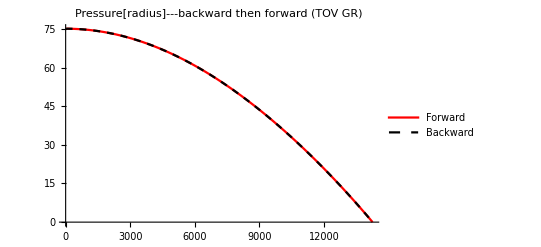

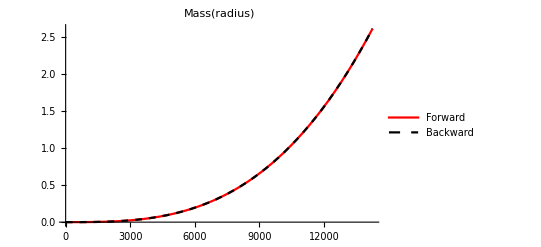

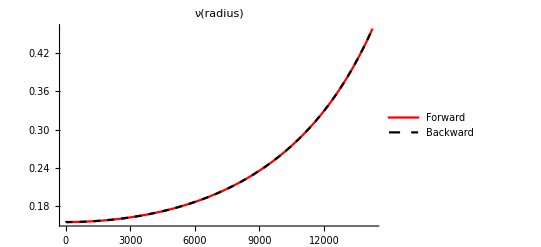

```mathematica
Plot[{po[r],poo[r]},{r,r0,r00},PlotRange->All,PlotLabel->"Pressure[radius]---backward then forward (TOV GR)",PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Forward","Backward"}]
Plot[{mo[r]/MSS,moo[r]/MSS},{r,r0,r00},PlotRange->All,PlotLabel->Mass[radius],PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Forward","Backward"}]
Plot[{Exp[νo[r]],Exp[νoo[r]]},{r,r0,r00},PlotRange->All,PlotLabel->ν[radius],PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Forward","Backward"}]
```

Keluarin datanya

```mathematica
ClearAll[x,data]
x[i_]:=r0+i(r00-r0)/1000
data:=Table[{x[i]/1000,poo[x[i]],po[x[i]],moo[x[i]]/MSS,mo[x[i]]/MSS,Exp[νoo[x[i]]],Exp[νo[x[i]]]},{i,0,1000}]
Export[FileNameJoin[{NotebookDirectory[],"TOV-reverse-4.2.dat"}],data]
```

C:\Users\ilham\Dropbox\00 SCGrav\ceknumerik\TOV-reverse-4.2.dat